# Aviation Formulae

## Preliminaries

## The Atmosphere

The atmosphere is described by a bipartite model, with one descriptor that applies from ground to the bottom of the stratosphere, and another descriptor that applies in the stratosphere.  This is because the temperature changes below the stratosphere and is constant in the stratosphere.

### Below the stratosphere

The stratosphere begins at 11000 meters and goes up far beyond the maximum altitude of commercial aircraft.  11000 meters is 36089 feet.

We will need the air density as a function of altitude for almost all of our calculations.  At sea level and 15 degrees C, the density is 1.225 kg/m^3.  There are correction factors for nonstandard sea level temperatures and lapse rates (rate of temp change with altitude), they will be ignored for now. Solving the ideal gas equilibrium condition below 11 kilometers gives the air density ratio (the ratio of density at altitude to density at sea level) as

```mathematica
densitylowratio[h_]:=(1-2.25577 10^-5 h)^4.25588
```

```mathematica
pressurelowratio[h_]:=(1-2.25577 10^-5 h)^5.25588
```

```mathematica
densityhighratio[pz]//CForm
```

0.297369*Power(E,0.00015768145193080938*(11000 - pz))

Solve for the definition of the pressure at the tropopause to find the altitude at the tropopause for consistency's sake.

```mathematica
Solve[1013.25 pressurelowratio[h] == 226.321,h]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{h→11000.}}

We'll also need the speed of sound as a function of altitude, which means a function of temp:

```mathematica
sound[temp_]:=331.318 Sqrt[1+ temp/273.15]
```

At the tropopause

```mathematica
sound[-56.5]
```

295.069

```mathematica
isasound[alt_]:=If[alt<=11000, 331.318 Sqrt[1+ (15-.0065 alt)/273.15],331.318 Sqrt[1-56.5/273.15]]
```

Find the transition altitude between IAS and Mach for different combinations of descent IAS and Mach.  Square the difference between the airspeed expressions for each and solve for where they are equal as a function of altitude.

```mathematica
transitionaltitude[speedias_,mach_]:=FindMinimum[(mach  331.318 Sqrt[1+ (15-.0065 alt)/273.15]-speedias Sqrt[1/densitylowratio[alt]])^2,alt][[2,1,2]]
```

Sample

```mathematica
transitionaltitude[320 .5144,.834]
```

8299.08

Graphically:

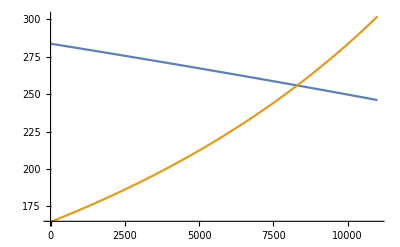

```mathematica
Plot[{.834  331.318 Sqrt[1+ (15-.0065 alt)/273.15],320 .5144 Sqrt[1/densitylowratio[alt]]},{alt, 0,11000}]
```

### In the stratosphere

In the stratosphere (above 11000 meters) the equation of state changes, and the density ratio is given by:

```mathematica
densityhighratio[h_]:=0.297369 Exp[-(h-11000)/6341.9]
```

```mathematica
density[h_]:=If[h<11000, densitylowratio[h],densityhighratio[h]] 1.2922
```

```mathematica
densityratio[h_]:=If[h<11000, densitylowratio[h],densityhighratio[h]]
```

Sqrt of density gives velocity multiplier to keep same CAS as sea level

```mathematica
1/Sqrt[densityratio[11000]]
```

1.8338

### A plot with a barely perceptible kink

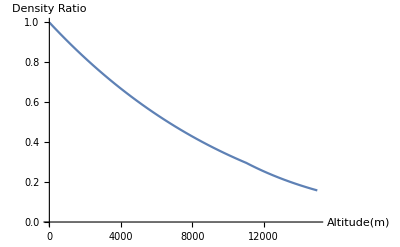

```mathematica
plot1=Plot[densityratio[h], {h,0,15000},AxesLabel->{"Altitude(m)", "Density Ratio"},PlotRange->{{0,15000},{0,1.0}}]
```

Compute a polynomial approximation to the atmospheric density ratio for a cruise altitude range.

```mathematica
atmoapprox=Fit[Table[{h,densityratio[h]^2}, {h,9000,13000,.01}], {1,x,x^2},x]
invatmoapprox=Fit[Table[{h,1/densityratio[h]}, {h,9000,13000,.01}], {1,x,x^2},x]
```

0.598957-0.0000685576 x+2.00464×10^-9 x^2

5.47228-0.000869716 x+6.17997×10^-8 x^2

Fit error < 1%

```mathematica
(atmoapprox/.x->9000)/densityratio[9000]^2
(atmoapprox/.x->11000)/densityratio[11000]^2
(atmoapprox/.x->13000)/densityratio[13000]^2
(invatmoapprox/.x->9000)densityratio[9000]
(invatmoapprox/.x->11000)densityratio[11000]
(invatmoapprox/.x->13000)densityratio[13000]
```

0.995782

0.988206

0.987909

1.00907

1.00605

1.00011

```mathematica
cruisedensityratioapprox[alt_]:=.8178-5.357 10^-5 alt+5.541 10^-10 alt^2
```

```mathematica
cruisedensityratiosapprox[alt_]:=.6020-6.899 10^-5 alt + 2.019 10^-9 alt^2
```

## Aircraft Performance (from BADA documentation)

## Lift and Drag

A set of numbers is required to quantify the aerodynamic performance of a given aircraft independent of its engine  parameters under several different operating regimes (climb, cruise, flaps at various extensions, dirty (gear down), clean, etc).  The simplest approximation to the Lift/Drag relationship is a quadratic equation, which works well if one is in a smooth operating regime far from stall and turbulence.  In addition, we need the effective wing area to compute lift, the reference aircraft mass (to know how much lift we need to stay aloft), the speed of the aircraft (which affects aerodynamic forces and engine performance), the density of the atmosphere (to compute magnitudes of lift and drag), and the acceleration of the aircraft in forward and transverse directions.

The lift is given by the fraction of the "flat plane" force required to balance the force of gravity on the aircraft where m is the mass of the aircraft in kg, h is altitude (meters), v is speed in meters/sec, s is wing area in meters^2, and ϕ is the bank angle. (banking reduces the effective lifting area, thereby increasing the amount of lift required per unit area, which in turn generates more induced drag).  The equations can be divided into aircraft specific constants (name with prefix ac), physics performance variables (with prefix p), and physical constants.  (real numerical values)  The preliminary version of the lift coefficient is:

```mathematica
clprelim[acm_,pvx_,pz_,pϕ_,acs_]:=2 acm 9.80665/(density[pz] pvx^2 acs Cos[pϕ])
```

```mathematica
clprelim[m,v,h,phi,S]
```

(0.000247067 m Sec[phi])/(S If[h<11000,densitylowratio[h],densityhighratio[h]])

Cos[ϕ] can be computed as a function of parametric representations of x and y velocities and accelerations inducing the banking after one calculates the parametric radius of curvature of the trajectory.  The turn radius R in meters is given by:

```mathematica
rxy[pvx_,pay_]:=pvx^2/pay
```

where pvx is in m/s and pay is in m/s^2.

A sample of a radius at typical speeds and a very gentle acceleration yields a big radius:

```mathematica
rxy[240,1]
```

57600

A harder bank yields a smaller circle

```mathematica
rxy[240,10]
```

5760

The  cosine of the arctan of v^2/gR (the bank angle) is a non-trigonometric function that emerges from the combination of two trig functions:

```mathematica
cphi[pvx_,pay_]:=Cos[ArcTan[pvx^2/(9.80665 rxy[pvx,pay])]]
```

A sample of a slight bank:

```mathematica
cphi[240,1]
```

0.994841

Banking hard enough to produce a centripetal force in the x-y plane equal to that of gravity in the z direction should produce a 45 degree bank angle and therefore a cosine equal to 1/Sqrt[2], a useful check for correctness of the formula.

```mathematica
cphi[240,9.80665]
```

0.707107

```mathematica
1/Sqrt[2.]
```

0.707107

Building up Fuel Burn equations

Now the lift coefficient is fully parametrized

```mathematica
cl[acm_,pz_,acs_,pvx_]:=2 acm 9.80665/(density[pz] pvx^2 acs )
```

```mathematica
cl[ma,ha,sa,vx]
```

(15.1782 ma)/(sa vx^2 If[ha<11000,densitylowratio[ha],densityhighratio[ha]])

But we need drag to know how much thrust (and therefore how much fuel we need to burn) is required.  The coefficients of drag and lift are related to lowest order by the "drag polar" (the quadratic relation mentioned in the introduction)

```mathematica
cd[accd0_,accd2_,acm_,pz_,pvx_,acs_]:=accd0+accd2 cl[acm,pz,acs,pvx]^2
```

```mathematica
cd[accd0,accd2,acm,pz,pvx,acs]
```

accd0+(230.378 accd2 acm^2)/(acs^2 pvx^4 If[pz<11000,densitylowratio[pz],densityhighratio[pz]]^2)

The drag is given by (in MKS units, where speed pvx is in m/sec, wing area acs in meters^2, altitude pz in meters)

```mathematica
drag[pz_,acs_, accd0_,accd2_,acm_,pvx_]:=1/2 density[pz] pvx^2 acs cd[accd0,accd2,acm,pz,pvx,acs]
```

```mathematica
drag[h,S,cd0,cd2,m,vx]
```

0.6461 S vx^2 (cd0+(230.378 cd2 m^2)/(S^2 vx^4 If[h<11000,densitylowratio[h],densityhighratio[h]]^2)) If[h<11000,densitylowratio[h],densityhighratio[h]]

```mathematica
drag[10000,  124.65, .0254, .0358,65300,240]
```

49090.2

Produce L/D plot using drag calculation, nominal mass

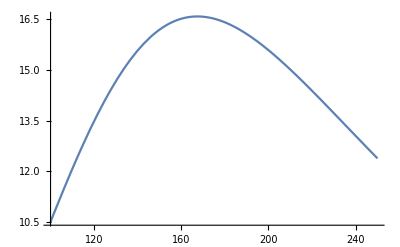

```mathematica
Plot[65300 9.80665/drag[10000,  124.65, .0254, .0358,65300,v],{v,100,250}]
```

```mathematica
.78 isasound[36390/3.28084]
```

230.154

```mathematica
FindMaximum[vx/drag[36390/3.28084,  124.65, .0254, .0358,62000,vx],{vx,160}]
```

{0.0054353,{vx→230.141}}

```mathematica
climbcruise={{62000,36390,230.1},
{63000,36040,230.1},
{64000,35710, 230.5},
{65000,35390,230.9},
{66000,35060,231.2},
{67000,34750,231.6},
{68000,34440,231.9},
{69000,34130,232.2},
{70000,33820,232.5},
{71000,33520,232.8},
{72000,33230,233.1},
{73000,32930,233.5},
{74000,32640,233.8},
{75000,32360,234.0},
{76000,32060,234.3}}
```

{{62000,36390,230.1},{63000,36040,230.1},{64000,35710,230.5},{65000,35390,230.9},{66000,35060,231.2},{67000,34750,231.6},{68000,34440,231.9},{69000,34130,232.2},{70000,33820,232.5},{71000,33520,232.8},{72000,33230,233.1},{73000,32930,233.5},{74000,32640,233.8},{75000,32360,234.},{76000,32060,234.3}}

```mathematica
fbcc=Table[fburn[climbcruise[[i,2]]/3.28084,124.65,.0254,.0358,.701, 1068,climbcruise[[i,1]],0,
climbcruise[[i,3]],0,0],{i,15}]
```

{fburn[11091.7,124.65,0.0254,0.0358,0.701,1068,62000,0,230.1,0,0],fburn[10985.,124.65,0.0254,0.0358,0.701,1068,63000,0,230.1,0,0],fburn[10884.4,124.65,0.0254,0.0358,0.701,1068,64000,0,230.5,0,0],fburn[10786.9,124.65,0.0254,0.0358,0.701,1068,65000,0,230.9,0,0],fburn[10686.3,124.65,0.0254,0.0358,0.701,1068,66000,0,231.2,0,0],fburn[10591.8,124.65,0.0254,0.0358,0.701,1068,67000,0,231.6,0,0],fburn[10497.3,124.65,0.0254,0.0358,0.701,1068,68000,0,231.9,0,0],fburn[10402.8,124.65,0.0254,0.0358,0.701,1068,69000,0,232.2,0,0],fburn[10308.3,124.65,0.0254,0.0358,0.701,1068,70000,0,232.5,0,0],fburn[10216.9,124.65,0.0254,0.0358,0.701,1068,71000,0,232.8,0,0],fburn[10128.5,124.65,0.0254,0.0358,0.701,1068,72000,0,233.1,0,0],fburn[10037.1,124.65,0.0254,0.0358,0.701,1068,73000,0,233.5,0,0],fburn[9948.67,124.65,0.0254,0.0358,0.701,1068,74000,0,233.8,0,0],fburn[9863.33,124.65,0.0254,0.0358,0.701,1068,75000,0,234.,0,0],fburn[9771.89,124.65,0.0254,0.0358,0.701,1068,76000,0,234.3,0,0]}

```mathematica
cruiseclimb=Table[Join[climbcruise[[i]],{fbcc[[i]]}],{i,15}]
```

{{62000,36390,230.1,fburn[11091.7,124.65,0.0254,0.0358,0.701,1068,62000,0,230.1,0,0]},{63000,36040,230.1,fburn[10985.,124.65,0.0254,0.0358,0.701,1068,63000,0,230.1,0,0]},{64000,35710,230.5,fburn[10884.4,124.65,0.0254,0.0358,0.701,1068,64000,0,230.5,0,0]},{65000,35390,230.9,fburn[10786.9,124.65,0.0254,0.0358,0.701,1068,65000,0,230.9,0,0]},{66000,35060,231.2,fburn[10686.3,124.65,0.0254,0.0358,0.701,1068,66000,0,231.2,0,0]},{67000,34750,231.6,fburn[10591.8,124.65,0.0254,0.0358,0.701,1068,67000,0,231.6,0,0]},{68000,34440,231.9,fburn[10497.3,124.65,0.0254,0.0358,0.701,1068,68000,0,231.9,0,0]},{69000,34130,232.2,fburn[10402.8,124.65,0.0254,0.0358,0.701,1068,69000,0,232.2,0,0]},{70000,33820,232.5,fburn[10308.3,124.65,0.0254,0.0358,0.701,1068,70000,0,232.5,0,0]},{71000,33520,232.8,fburn[10216.9,124.65,0.0254,0.0358,0.701,1068,71000,0,232.8,0,0]},{72000,33230,233.1,fburn[10128.5,124.65,0.0254,0.0358,0.701,1068,72000,0,233.1,0,0]},{73000,32930,233.5,fburn[10037.1,124.65,0.0254,0.0358,0.701,1068,73000,0,233.5,0,0]},{74000,32640,233.8,fburn[9948.67,124.65,0.0254,0.0358,0.701,1068,74000,0,233.8,0,0]},{75000,32360,234.,fburn[9863.33,124.65,0.0254,0.0358,0.701,1068,75000,0,234.,0,0]},{76000,32060,234.3,fburn[9771.89,124.65,0.0254,0.0358,0.701,1068,76000,0,234.3,0,0]}}

```mathematica
NSolve[D[vx/drag[36500/3.28084,  124.65, .0254, .0358,61700,vx],vx]==0,vx]
```

{{vx→-230.191},{vx→230.191},{vx→0.+230.191 ⅈ},{vx→0.-230.191 ⅈ}}

```mathematica
FindMaximum[vv/drag[10000,  124.65, .0254, .0358,65300,vv],vv]
```

{1.84819×10^-9,{vv→1.}}

Calculation of drag for Socata Trinidad (from BADA data), advanced light single, my stand-in for ODM aircraft

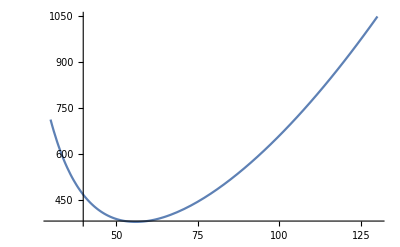

```mathematica
b=Plot[drag[2500,11.9, .01, .037, 1000, x],{x,30,130}]
```

Convert drag formula into energy required for a mission of d nautical miles at v knots for a Socata Trinidad type aircraft:

```mathematica
drag[2500,11.9, .01, .037, 1000, vx/1.85] dx 1852
```

3249.79 dx (0.01+(1.15561×10^6)/vx^4) vx^2

## Thrust Constraint

The maximum climb thrust is a quadratic polynomial in altitude (h).  It is given in general form as:

```mathematica
maxthrust[acc1_,acc2_,acc3_,pz_]:=acc1-acc1/acc2 pz+acc1 acc3 pz^2
```

where thrust is in Newtons (N), altitude (h) in ft,  c1 is in Newtons, c1/c2 in Newton-ft, c1 c3 in Newton/ft^2.  For our B-737-800, c1 = 146590 N, c2 = 53872 ft, c3 = 0.30453 10^-9/ft^2. Converting to a metric answer (using the non-metric or mixed constants above) gives:

```mathematica
maxthrustmetric[c1_,c2_,c3_,h_]:=c1-c1/c2 h 3.28084+c1 c3 h^2 10.7639
```

For the Boeing 737-800,

```mathematica
t737=maxthrustmetric[146590,53872,0.30453 10^(-10),h]
```

146590-8.92743 h+0.0000480512 h^2

```mathematica
t737/.h->10000
```

62120.9

A picture shows power fade, but does not show the improvement gained by going close to the speed of sound (Mach compression)  This may generate unrealistic optimizations.

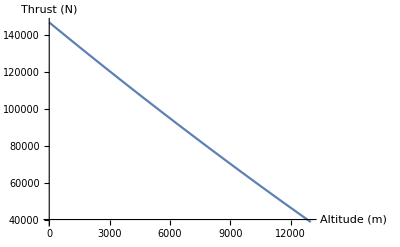

```mathematica
Plot[t737, {h, 0, 13000}, AxesLabel->{"Altitude (m)", "Thrust (N)"}]
```

Or, plotted as a fraction of maximum sea level thrust it becomes clear that there will be a maximum altitude beyond which there is insufficient thrust to overcome drag and continue climbing:

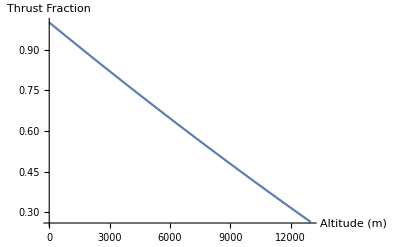

```mathematica
Plot[t737/146590., {h, 0, 13000},  AxesLabel->{"Altitude (m)", "Thrust Fraction"}]
```

## Fuel Burn

The BADA documentation gives us a fuel burn associated with a particular thrust and velocity.

```mathematica
fuelburn[pthrust_, pvx_,accf1_,accf2_]:= pthrust accf1 /60000(1 + pvx/(accf2 .5144))
```

It is a characteristic of a specific engine to have a maximum thrust (discussed in previous section), that when combined with velocity gives an associated maximum fuel burn.

```mathematica
maxfuelburn[c1_,c2_,c3_,pz_,pvx_,accf1_,accf2_]:=(c1-c1/c2 pz 3.28084+c1 c3 pz^2 10.7639) accf1 /60000(1 + pvx/(accf2 .5144))
```

Evaluate maxfuelburn for a B737-800:

```mathematica
maxfuelburn[146590,53872,0.30453 10^(-10),pz,pvx,.701,1068]
```

0.0000116833 (1+0.00182024 pvx) (146590-8.92743 pz+0.0000480512 pz^2)

```mathematica
Plot3D[maxfuelburn[146590,53872,0.30453 10^(-10),pz,pvx,.701,1068],{pz,0,13000},{pvx,100,240}]
```

-Graphics3D-

For Boeing 737-800, cf1 = .701, cf2 = 1068 kt (converted to m/sec in fuelburn[] above), the fuel burn in kg/sec is

```mathematica
fuelburn[40000, 240, .701, 1068]
```

0.671491

The maximum fuel burn is at very high speed and at sea level (an unflyable combination under normal circumstances), almost 2.5 kg/s.  This is about 21,600 lb/hr.

For descent, minimum fuel burn is

```mathematica
minfuelburn[ackc3_,ackc4_, pz_]:=1/60.(ackc3-.3048 ackc4/pz)
```

```mathematica
minfuelburn[14.19, 65932,pz]
```

0.0166667 (14.19-20096.1/pz)

There's a problem below 1500 meters as shown below.  Not sure what to do about it.  Perhaps just use asymptotic value of ackc3/60 kg/sec = 14.19/60= .2365 kg/sec and err on the consumptive side. (the right hand side of the plot below)

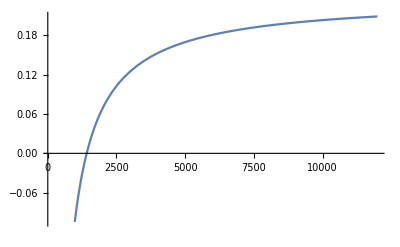

```mathematica
Plot[minfuelburn[14.19, 65932,h], {h, 100,12000}]
```

Total Energy Model

```mathematica
thrust[pz_,acs_,accd0_,accd2_,acm_,pvz_,pvx_,pax_ ]:=(acm 9.80665 pvz/pvx+ acm pax+drag[pz,acs,accd0,accd2,acm,pvx])
```

```mathematica
thrust[10000,124.65,.0254,.0358,65300,0,
240,0]
```

49090.2

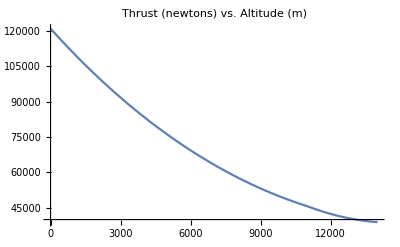

```mathematica
Plot[thrust[x, 124.65, .0254, .0358, 65300, 0, 240, 0], {x, 0, 14000}, PlotLabel->"Thrust (newtons) vs. Altitude (m)"]
```

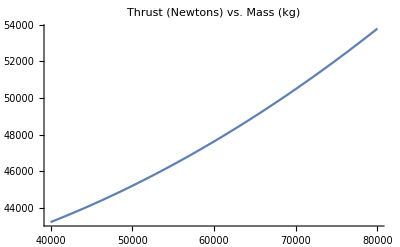

```mathematica
Plot[thrust[10000, 124.65, .0254, .0358, x, 0, 240, 0], {x, 40000, 80000}, PlotLabel->"Thrust (Newtons) vs. Mass (kg)"]
```

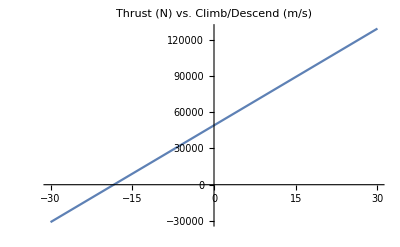

```mathematica
Plot[thrust[10000, 124.65, .0254, .0358, 65300, x, 240, 0], {x, -30, 30}, PlotLabel->"Thrust (N) vs. Climb/Descend (m/s)"]
```

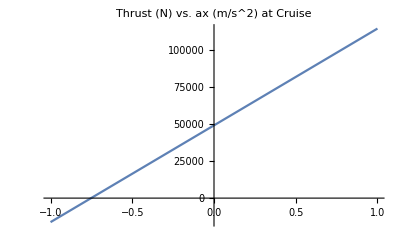

```mathematica
Plot[thrust[10000, 124.65, .0254, .0358, 65300, 0, 240, x], {x, -1,1}, PlotLabel->"Thrust (N) vs. ax (m/s^2) at Cruise"]
```

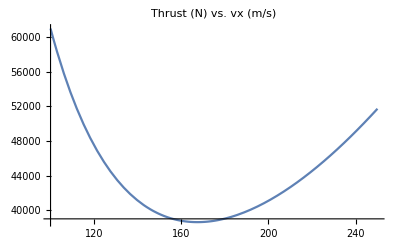

```mathematica
Plot[thrust[10000, 124.65, .0254, .0358, 65300, 0, x, 0], {x, 100, 250}, PlotLabel->"Thrust (N) vs. vx (m/s)"]
```

```mathematica
Plot3D[thrust[x, 124.65, .0254, .0358, 65300, 0, y, 0], {x, 0, 14000}, {y,100, 250}, PlotLabel->"Thrust (N) vs. h(m) and vx (m/s)"]
```

-Graphics3D-

which equals the drag computed above for the same mass and forward velocity.  If the plane is climbing, the thrust changes:

```mathematica
thrust[10000,124.65,.0254,.0358,65300,3,
240,0]
```

57094.8

or accelerating forward...

```mathematica
thrust[10000,124.65,.0254,.0358,65300,0,
240,0.25]
```

65415.2

or some of all of the above..

```mathematica
thrust[10000,124.65,.0254,.0358,65300,1,
240,.25]
```

68083.4

A simplified version for use in coding:

```mathematica
fburn[pz_,acs_,accd0_,accd2_,accf1_,accf2_,acm_,pvz_,pvx_,pax_]:=1/60000 accf1(acm 9.80665 pvz/pvx+ acm pax+drag[pz,acs,accd0,accd2,acm,pvx])(1 + pvx/(accf2 .5144))
```

```mathematica
TraditionalForm[fburn[pz,acs,accd0,accd2,accf1,accf2,acm,pvz,pvx,pax]]
```

1/60000 accf1 ((1.94401 pvx)/accf2+1) (0.6461 acs pvx^2 If[pz<11000,densitylowratio(pz),densityhighratio(pz)] ((230.378 accd2 acm^2)/(acs^2 pvx^4 If[pz<11000,densitylowratio(pz),densityhighratio(pz)]^2)+accd0)+acm pax+(9.80665 acm pvz)/pvx)

```mathematica
fburn[pz,acs,accd0,accd2,accf1,accf2,acm,pvz,pvx,pax]//CForm
```

(accf1*(1 + (1.944012441679627*pvx)/accf2)*
     (acm*pax + (9.80665*acm*pvz)/pvx + 
       0.6461*acs*Power(pvx,2)*
        (accd0 + (230.3784590617293*accd2*Power(acm,2))/
           (Power(acs,2)*Power(pvx,4)*
             Power(If(pz < 11000,densitylowratio(pz),
               densityhighratio(pz)),2)))*
        If(pz < 11000,densitylowratio(pz),densityhighratio(pz))))/
   60000.

```mathematica
b767fburn[alt_]:=fburn[alt, 283.3,.020,.0489,.662,1227,150000,0,310 .5144/Sqrt[densityratio[alt]],0]
a320fburn[alt_]:=fburn[alt,122.6,.0251,.0361,.633,859,64000,0,290 .5144/Sqrt[densityratio[alt]],0]
crj200fburn[alt_]:=fburn[alt,48.35,.0232,.0283,.583,383,20910,0,270 .5144/Sqrt[densityratio[alt]],0]
```

```mathematica
b767fburn[5000]
a320fburn[5000]
crj200fburn[5000]
```

1.69441

0.792246

0.296014

```mathematica
fburn[11000,124.65,.0254,.0358,.701, 1068,50000,0,
240,0]
```

0.692944

Slow down 2% a la Ryanair

```mathematica
fburn[11000,124.65,.0254,.0358,.701, 1068,50000,0,
235.2,0]
```

0.669872

```mathematica
fuelefficiency[pz_,acs_,accd0_,accd2_,accf1_,accf2_,acm_,pvz_,pvx_,pax_]:=fburn[pz,acs,accd0,accd2,accf1,accf2,acm,pvz,pvx,pax]/pvx
```

```mathematica
fuelefficiency[pz,acs,accd0,accd2,accf1,accf2,acm,pvz,pvx,0 ]//TraditionalForm
```

1/(60000 pvx)accf1 ((1.94401 pvx)/accf2+1) (0.6461 acs pvx^2 If[pz<11000,densitylowratio(pz),densityhighratio(pz)] ((230.378 accd2 acm^2)/(acs^2 pvx^4 If[pz<11000,densitylowratio(pz),densityhighratio(pz)]^2)+accd0)+(9.80665 acm pvz)/pvx)

```mathematica
fuelefficiency[z,124.65,.0254,.0358,.701, 1068,m,Subscript[v, z],
Subscript[v, x],0]//TraditionalForm
```

1/(247.858_x)0.0000116833 (0.00182024 247.858_x+1) (80.5364 247.858_x^2 If[z<11000,densitylowratio(z),densityhighratio(z)] ((0.000530812 m^2)/(247.858_x^4 If[z<11000,densitylowratio(z),densityhighratio(z)]^2)+0.0254)+(9.80665 m 247.858_z)/(247.858_x))

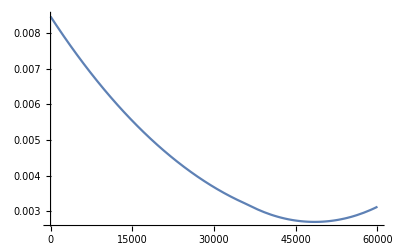

```mathematica
Plot[fuelefficiency[y/3.28,124.65,.0254,.0358,.701, 1068,65300,0,
240,0],  {y, 0, 60000}]
```

```mathematica
Minimize[fuelefficiency[y/3.28,124.65,.0254,.0358,.701, 1068,65300,0,
240,0],y]
```

{0.00270141,{y→48473.4}}

```mathematica
Plot3D[fuelefficiency[x,124.65,.0254,.0358,.701, 1068,65300,0,
y,0], {x, 0, 14000}, {y, 100, 250}, PlotLabel->"Fuel Efficiency(kg/m) ",AxesLabel->{"Altitude(m)","Speed(m/sec)"}]
```

-Graphics3D-

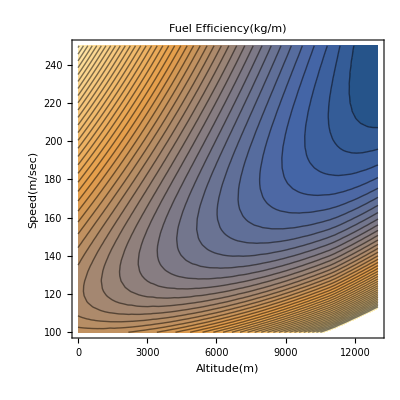

```mathematica
ContourPlot[fuelefficiency[x,124.65,.0254,.0358,.701, 1068,65300,0,
y,0], {x, 0, 13000}, {y, 100, 250}, PlotLabel->"Fuel Efficiency(kg/m) ",AxesLabel->{"Altitude(m)","Speed(m/sec)"},Contours->40]
```

Airspeed Conversions

Converting between true airspeed and calibrated airspeed:

```mathematica
vtas[vcas_]:=((2/μ)( p/ρ)((1 + (p0/p) ((1 + (μ/2)( ρ0/p0)vcas^2)^(1/μ)-1))^μ-1))^(1/2)/.μ->2/7
```

```mathematica
vtas[Sqrt[x]]
```

√7 √((p (-1+(1+(p0 (-1+(1+(x ρ0)/(7 p0))^(7/2)))/p)^(2/7)))/ρ)

```mathematica
Series[vtas[Sqrt[x]], {x, 0,2}]
```

√(ρ0/ρ) √x+(5 (p-p0) ρ0 √(ρ0/ρ) x^(3/2))/(56 p p0)+O[x]^(5/2)

```mathematica
vcas[vtas_]:=((2/μ) (p0/ρ0)((1+(p/p0)((1 + (μ/2)(ρ/p) vtas^2)^(1/μ)-1))^μ-1))^(1/2)/.μ->2/7
```

```mathematica
vcas[y]
```

√7 √((p0 (-1+(1+(p (-1+(1+(y^2 ρ)/(7 p))^(7/2)))/p0)^(2/7)))/ρ0)

```mathematica
Series[vcas[y], {y,0,5}]
```

√(ρ/ρ0) y-(5 ((p-p0) ρ √(ρ/ρ0)) y^3)/(56 (p p0))+(15 (9 p^2-10 p p0+p0^2) ρ^2 √(ρ/ρ0) y^5)/(6272 p^2 p0^2)+O[y]^6

Compute descent angles using sea-level drag equation to get IAS (Indicated Airspeed)

What indicated speed does optimal L/D occur at?

```mathematica
FindMinimum[ drag[0,  124.65, .0254, .0358,65300,vel],vel]
```

{38620.9,{vel→97.159}}

Pretty slow

```mathematica
97.159  meter/s 1.94384 knots/(meter/s)
```

{{188.862 knots}}

Compute the descent rise/run for different IAS.

```mathematica
riserun=Table[{vel,drag[0,  124.65, .0254, .0358,65300,vel/1.94384]/(65300 9.80665)}, {vel, 250,320,10}]
```

{{250,0.070048},{260,0.0730612},{270,0.0763852},{280,0.0799999},{290,0.0838889},{300,0.0880385},{310,0.0924369},{320,0.0970745}}

This translates into a descent rate (sea level) that can be integrated with the appropriate density factor to get a descent time.  As derived elsewhere from the analysis of the parabolic drag polar, the minimum sink rate is different than the best L/D by 32% (3^ (1/4) - 1).  Both of these optima appear to be uneconomically slow, so descents are typically much faster.

```mathematica
3^(1/4.)
```

1.31607

Slowest descent will occur at a speed given by (best L/D speed) / (3**(1/4)), which will be very slow. It may be so close to stall that the parabolic approximation to the drag polar is no longer valid.

```mathematica
188.862/3^(1/4) knots
```

143.504 knots

Descent rates in feet per second at sea level for different descent rates (250kn: 10: 320kn).  At higher altitudes, 
descent rates scale by 1/Sqrt[density], as the descent angle stays the same.

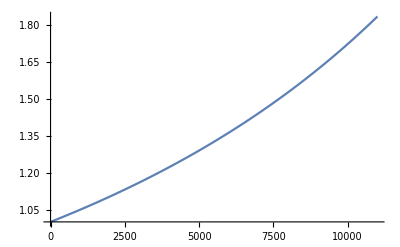

```mathematica
Plot[Sqrt[1/densitylowratio[z]] , {z,0,11000}]
```

Compute the times required for the constant IAS descent and the distances covered., in seconds and meters.

Figure out deceleration from descent IAS to 250 knots for 10000 ft FAA speed limit.  Use the numerical differential equation solver NDSolve[]

```mathematica
leveldrag=drag[10000/3.2808,  124.65, .0254, .0358,65300,y[t]/Sqrt[densitylowratio[10000/3.28084]]1/1.94384]
```

21.3142 (0.0254+(3.23156×10^7)/y[t]^4) y[t]^2

```mathematica
s=NDSolve[{y'[t]==-leveldrag/(65300 ), y[0]==290 1/Sqrt[densitylowratio[10000/3.2808]]1/1.94384},y,{t,0,80}]
```

{{y→InterpolatingFunction[{{0., 80.}}, <>]}}

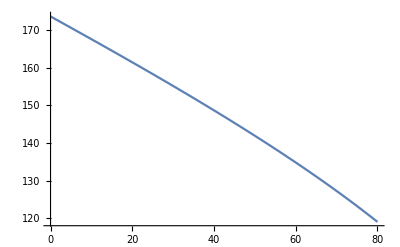

```mathematica
Plot[Evaluate[y[t]/.s],{t,0,80},PlotRange->All]
```

True airspeed at 10k feet, 250 knots CAS

```mathematica
250/Sqrt[densitylowratio[10000/3.2808]] 1/1.94384
```

149.662

```mathematica
Evaluate[y[39]/.s]
```

{149.31}

This is how far the aircraft needs to coast to burn off speed from CAS 290 -> 250 in meters

```mathematica
NIntegrate[y[t]/.s, {t,0,39}]
```

{6304.15}

Format the level off data at 10000 feet in terms of approach speed above 10k (knots), time to slow down (sec), and distance to slow down (meters)

```mathematica
leveloffcoast = {{250, 0, 0}, {260, 9.3, 1420}, {270, 18.9, 2942}, {280, 28.5, 4524}, {290, 38.5, 6229}, {300, 48.5, 7995}, {310, 58.6, 9839}, {320, 68.7, 11744}}
```

{{250,0,0},{260,9.3,1420},{270,18.9,2942},{280,28.5,4524},{290,38.5,6229},{300,48.5,7995},{310,58.6,9839},{320,68.7,11744}}

Compute the Mach descent portion of the flight.  True airspeed will be close to constant, but IAS will not be.  Distances in meters.

```mathematica
vmach[mconst_,alt_]:=mconst  isasound[alt]
```

Compute total times and distances to arrive at 10k, 250 knots from Top of Descent at FL360.

Figure out fuel efficiency (since we're distance based for this part) for level cruise at 10k feet, 250 knots IAS.

```mathematica
tenburn738=fuelefficiency[10000/3.2808,124.65,.0254,.0358,.701, 1068,65300,0,
250/(1.9434 Sqrt[densityratio[10000/3.2808]]),0,0]
```

fuelefficiency[3048.04,124.65,0.0254,0.0358,0.701,1068,65300,0,149.696,0,0]

That actual speed in meters/sec is

```mathematica
250 knots/(1.9434 knots/(meters/sec)Sqrt[densityratio[10000/3.2808]])
```

(149.696 meters)/sec

Look up idle fuel burn in kg/sec

```mathematica
idleburn=.2365
```

0.2365

Computations for Rick and ANZ problem

Compute idle thrust at 10k ft and velocity expressed in KIAS for the purpose of calculating deceleration time/distance.

What's the speed limit altitude of 10k ft in meters?

```mathematica
10000/3.28084
```

3048.

```mathematica
fuelburn[pthrust_, pvx_,accf1_,accf2_]:= pthrust accf1 /60000(1 + pvx/(accf2 .5144))
```

```mathematica
Solve[26.872/60==fuelburn[thrust,vias .5144/Sqrt[densitylowratio[3048]],.4916,487.93],thrust]
```

{{thrust→54662.3/(1.+0.00238492 vias)}}

A simplified version, assuming thrust is constant and is same as 250 kn (10% error between 320 and 240 KIAS)

```mathematica
NSolve[26.872/60==fuelburn[thrust,250 .5144/Sqrt[densitylowratio[3048]],.4916,487.93],thrust]
```

{{thrust→34244.7}}

Compute drag in level flight at 10k ft.

```mathematica
leveldrag=drag[10000/3.2808,  428.04,.016943,.048939,237600,y[t]/Sqrt[densitylowratio[10000/3.28084]]1/1.94384]
```

73.1916 (0.016943+(4.95983×10^7)/y[t]^4) y[t]^2

Create a differential equation for deceleration at 10k ft with initial conditions of descent speed in KIAS, with the goal of ending up at 250 knots IAS.  Solve this numerically, extract times and distances for slowdown.  Include idle thrust

```mathematica
s=NDSolve[{y'[t]==(-leveldrag+34245)/(237600 ), y[0]==310 1/Sqrt[densitylowratio[10000/3.2808]]1/1.94384},y,{t,0,80}]
```

{{y→InterpolatingFunction[{{0., 80.}}, <>]}}

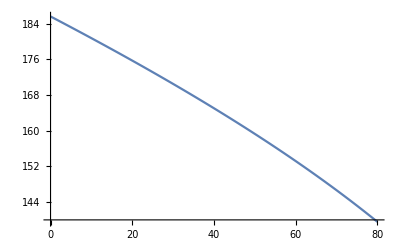

```mathematica
Plot[Evaluate[y[t]/.s],{t,0,80},PlotRange->All]
```

Get boundary conditions for speed at end of deceleration in m/s.

```mathematica
250/Sqrt[densitylowratio[10000/3.2808]] 1/1.94384
```

149.662

```mathematica
slowdownsolve=NSolve[Evaluate[y[x]/.s]==149.662,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→65.4646}}

```mathematica
slowdownsolve[[1,1,2]]
```

65.4646

```mathematica
NIntegrate[y[t]/.s, {t,0,slowdownsolve[[1,1,2]]}][[1]]
```

11033.9

```mathematica
slowdown777 = {{250, 8.8, 1291},{260,18.3,2741},{270, 28.4, 4344},{280,39.2,6120},{290, 50.4, 8033},{300,62.3,10132},{310,74.6,12378},{320, 87.8, 14850}}
```

{{250,8.8,1291},{260,18.3,2741},{270,28.4,4344},{280,39.2,6120},{290,50.4,8033},{300,62.3,10132},{310,74.6,12378},{320,87.8,14850}}

```mathematica
fburn[pz,acs,accd0,accd2,accf1,accf2,acm,pvz,pvx,pax]/pvx
```

1/(60000 pvx)accf1 (1+(1.94401 pvx)/accf2) (acm pax+(9.80665 acm pvz)/pvx+0.6461 acs pvx^2 (accd0+(230.378 accd2 acm^2)/(acs^2 pvx^4 If[pz<11000,densitylowratio[pz],densityhighratio[pz]]^2)) If[pz<11000,densitylowratio[pz],densityhighratio[pz]])

Data for a 737-800 glide at idle thrust.

## Numerical Integrations for Descent

```mathematica
glidedata737[ias_]:=
{
record = Table[{}, {130}]; (*Where to put numerical integration results *)

(*Density factor for changing density below tropopause*)
vdvdh = ias .5144/Sqrt[densitylowratio[h]] D[ias .5144/ Sqrt[densitylowratio[h]], h]/9.808;

(*Density factor for changing density in stratosphere*)highvdvdh = ias .5144/Sqrt[densityhighratio[h]] D[ias .5144/ Sqrt[densityhighratio[h]], h]/9.808;

(*Discrete solver *)
i = 1;
Do[
{
a  = (* Force balance at low alt to solve for descent rate vz(h) *)NSolve[ 1 14.19/60 ==fburn[h,124.65,.0254,.0358,.701, 1068,65300,vz,
ias .5144/Sqrt[densitylowratio[h]],0], vz][[1,1,2]];
  ah= (* Force balance at high alt to solve for descent rate vz(h) *)NSolve[ 1 14.19/60 ==fburn[h,124.65,.0254,.0358,.701, 1068,65300,vz,
ias .5144/Sqrt[densityhighratio[h]],0], vz][[1,1,2]];

b = ias .5144/Sqrt[densitylowratio[h]];(* Convert to true airspeed in m/s *)
bh= ias .5144/Sqrt[densityhighratio[h]];
c = h;
d = b/a;
dh = bh/ah;
e = 1 +vdvdh;
eh=1+highvdvdh; (* Constant CAS in the stratosphere is rare *)
If[h<11000,record[[i]]={-100 e/a,b,c,-d,- d  e},record[[i]]={-100 eh/ah, bh, c, -dh,-dh eh}];
i = i+1;

},{h,50,12950,100} (* Bins 100m wide from sea level to 13000 m *)
]; 
Reverse[record]
}[[1]]
```

```mathematica
glidedata737m[ias_, mass_]:=
{
record = Table[{}, {130}]; (*Where to put numerical integration results *)

(*Density factor for changing density below tropopause*)
vdvdh = ias .5144/Sqrt[densitylowratio[h]] D[ias .5144/ Sqrt[densitylowratio[h]], h]/9.808;

(*Density factor for changing density in stratosphere*)highvdvdh = ias .5144/Sqrt[densityhighratio[h]] D[ias .5144/ Sqrt[densityhighratio[h]], h]/9.808;

(*Discrete solver *)
i = 1;
Do[
{
a  = (* Force balance at low alt to solve for descent rate vz(h) *)NSolve[ 1 14.19/60 ==fburn[h,124.65,.0254,.0358,.701, 1068,mass,vz,
ias .5144/Sqrt[densitylowratio[h]],0], vz][[1,1,2]];
  ah= (* Force balance at high alt to solve for descent rate vz(h) *)NSolve[ 1 14.19/60 ==fburn[h,124.65,.0254,.0358,.701, 1068,mass,vz,
ias .5144/Sqrt[densityhighratio[h]],0], vz][[1,1,2]];

b = ias .5144/Sqrt[densitylowratio[h]];(* Convert to true airspeed in m/s *)
bh= ias .5144/Sqrt[densityhighratio[h]];
c = h;
d = b/a;
dh = bh/ah;
e = 1 +vdvdh;
eh=1+highvdvdh; (* Constant CAS in the stratosphere is rare *)
If[h<11000,record[[i]]={-100 e/a,b,c,-d,- d  e},record[[i]]={-100 eh/ah, bh, c, -dh,-dh eh}];
i = i+1;

},{h,50,12950,100} (* Bins 100m wide from sea level to 13000 m *)
]; 
Reverse[record]
}[[1]]
```

Input values for a 777-300, equate idle thrust forces and solve for descent rate at constant CAS

```mathematica
glidedata777[ias_]:=
{
record = Table[{}, {130}]; (*Where to put numerical integration results *)

(*Density factor for changing density below tropopause*)
vdvdh = ias .5144/Sqrt[densitylowratio[h]] D[ias .5144/ Sqrt[densitylowratio[h]], h]/9.808;

(*Density factor for changing density in stratosphere*)highvdvdh = ias .5144/Sqrt[densityhighratio[h]] D[ias .5144/ Sqrt[densityhighratio[h]], h]/9.808;

(*Discrete solver *)
i = 1;
Do[
{
a  = (* Force balance at low alt to solve for descent rate vz(h) *)NSolve[ 26.872/60 ==fburn[h,428.04,.016943,.048939,.4916,487.93,237600,vz,ias .5144/Sqrt[densitylowratio[h]],0], vz][[1,1,2]];
  ah= (* Force balance at high alt to solve for descent rate vz(h) *)NSolve[ 1 26.872/60 ==fburn[h,428.04,.016943,.048939,.4916,487.93,237600,vz,ias .5144/Sqrt[densityhighratio[h]],0], vz][[1,1,2]];

b = ias .5144/Sqrt[densitylowratio[h]];(* Convert to true airspeed in m/s *)
bh= ias .5144/Sqrt[densityhighratio[h]];
c = h;
d = b/a;
dh = bh/ah;
e = 1 +vdvdh;
eh=1+highvdvdh; (* Constant CAS in the stratosphere is rare *)
If[h<11000,record[[i]]={-100 e/a,b,c,-d,- d  e},record[[i]]={-100 eh/ah, bh, c, -dh,-dh eh}];
i = i+1;

},{h,50,12950,100} (* Bins 100m wide from sea level to 13000 m *)
]; 
Reverse[record]
}[[1]]
```

```mathematica
glidedata777m[ias_, mass_]:=
{
record = Table[{}, {130}]; (*Where to put numerical integration results *)

(*Density factor for changing density below tropopause*)
vdvdh = ias .5144/Sqrt[densitylowratio[h]] D[ias .5144/ Sqrt[densitylowratio[h]], h]/9.808;

(*Density factor for changing density in stratosphere*)highvdvdh = ias .5144/Sqrt[densityhighratio[h]] D[ias .5144/ Sqrt[densityhighratio[h]], h]/9.808;

(*Discrete solver *)
i = 1;
Do[
{
a  = (* Force balance at low alt to solve for descent rate vz(h) *)NSolve[ 26.872/60 ==fburn[h,428.04,.016943,.048939,.4916,487.93,mass,vz,ias .5144/Sqrt[densitylowratio[h]],0], vz][[1,1,2]];
  ah= (* Force balance at high alt to solve for descent rate vz(h) *)NSolve[ 1 26.872/60 ==fburn[h,428.04,.016943,.048939,.4916,487.93,mass,vz,ias .5144/Sqrt[densityhighratio[h]],0], vz][[1,1,2]];

b = ias .5144/Sqrt[densitylowratio[h]];(* Convert to true airspeed in m/s *)
bh= ias .5144/Sqrt[densityhighratio[h]];
c = h;
d = b/a;
dh = bh/ah;
e = 1 +vdvdh;
eh=1+highvdvdh; (* Constant CAS in the stratosphere is rare *)
If[h<11000,record[[i]]={-100 e/a,b,c,-d,- d  e},record[[i]]={-100 eh/ah, bh, c, -dh,-dh eh}];
i = i+1;

},{h,50,12950,100} (* Bins 100m wide from sea level to 13000 m *)
]; 
Reverse[record]
}[[1]]
```

```mathematica
m777={159600,237500,299300}
```

{159600,237500,299300}

```mathematica
m737={41150,65300,78300}
```

{41150,65300,78300}

```mathematica
twowts[list_]:={(list[[1]]+list[[2]])/2,(list[[2]]+list[[3]])/2}
```

```mathematica
twowts[m737]
twowts[m777]
```

{53225,71800}

{198550,268400}

```mathematica
{198550,268400}
```

{198550,268400}

```mathematica
1/9.808 mach isasound[h] D[mach isasound[h],h]/. h->11000
```

-0.133166 mach^2

Solve for a 777-300 Mach descent

```mathematica
machdata777[machno_]:= (* Discrete solver for constant mach descent *)
{
record = Table[{}, {70}];
i = 1;
Do[
{

v = machno isasound[h]; (* Mach as a function of altitude *)
a  = (* Solve for descent rate vz(h) *)NSolve[ 1 26.872/60 ==fburn[h,428.04,.016943,.048939,.4916,487.93,237600,vz,v,0], vz][[1,1,2]];
c = h;
d = v/a;
e = If[h>11000, 1,1 -.133 machno^2]; (* Account for tropopause in deceleration factor *)
record[[i]]={-100 e/a, v, c, -d,-d e };
i = i+1;

},{h,6050,12950,100} (* Range from 7000 to 13000 meters in 100 m bins *)
]; 
Reverse[record]
}[[1]]
```

```mathematica
machdata777m[machno_,mass_]:= (* Discrete solver for constant mach descent *)
{
record = Table[{}, {70}];
i = 1;
Do[
{

v = machno isasound[h]; (* Mach as a function of altitude *)
a  = (* Solve for descent rate vz(h) *)NSolve[ 1 26.872/60 ==fburn[h,428.04,.016943,.048939,.4916,487.93,mass,vz,v,0], vz][[1,1,2]];
c = h;
d = v/a;
e = If[h>11000, 1,1 -.133 machno^2]; (* Account for tropopause in deceleration factor *)
record[[i]]={-100 e/a, v, c, -d,-d e };
i = i+1;

},{h,6050,12950,100} (* Range from 6000 to 13000 meters in 100 m bins *)
]; 
Reverse[record]
}[[1]]
```

Mach descent data for a 737-800

```mathematica
machdata737[machno_]:= (* Discrete solver for constant mach descent *)
{
record = Table[{}, {70}];
i = 1;
Do[
{

v = machno isasound[h]; (* Mach as a function of altitude *)
a  = (* Solve for descent rate vz(h) *)NSolve[ 1 14.19/60 ==fburn[h,124.65,.0254,.0358,.701, 1068,65300,vz,v,0], vz][[1,1,2]];
c = h;
d = v/a;
e = If[h>11000, 1,1 -.133 machno^2]; (* Account for tropopause in deceleration factor *)
record[[i]]={-100 e/a, v, c, -d,-d e };
i = i+1;

},{h,6050,12950,100} (* Range from 6000 to 13000 meters in 100 m bins *)
]; 
Reverse[record]
}[[1]]
```

```mathematica
machdata737m[machno_,mass_]:= (* Discrete solver for constant mach descent *)
{
record = Table[{}, {70}];
i = 1;
Do[
{

v = machno isasound[h]; (* Mach as a function of altitude *)
a  = (* Solve for descent rate vz(h) *)NSolve[ 1 14.19/60 ==fburn[h,124.65,.0254,.0358,.701, 1068,mass,vz,v,0], vz][[1,1,2]];
c = h;
d = v/a;
e = If[h>11000, 1,1 -.133 machno^2]; (* Account for tropopause in deceleration factor *)
record[[i]]={-100 e/a, v, c, -d,-d e };
i = i+1;

},{h,6050,12950,100} (* Range from 6000 to 13000 meters in 100 m bins *)
]; 
Reverse[record]
}[[1]]
```

## Profile Calculations

Compute fuel burn in level flight at 6k ft for 777.

```mathematica
fburn[10000,428.04,.016943,.048939,.4916,487.93,237600,0,240,0]
```

2.25091

```mathematica
fburn[6000/3.2808,428.04,.016943,.048939,.4916,487.93,237600,0,.5144 240/Sqrt[densitylowratio[6000/3.2808]],0]
```

1.69428

```mathematica
highlevelfb290=Table[{10000+1000 j,fburn[(10000+1000 j)/3.2808,428.04,.016943,.048939,.4916,487.93,237600,0,.5144 290/Sqrt[densitylowratio[(10000+1000 j)/3.2808]],0]Sqrt[densitylowratio[(10000+1000 j)/3.2808]]1944/(.5144 290)},{j,1,18}]
```

{{11000,22.674},{12000,22.4641},{13000,22.2559},{14000,22.0496},{15000,21.8449},{16000,21.6421},{17000,21.441},{18000,21.2417},{19000,21.0441},{20000,20.8483},{21000,20.6542},{22000,20.4619},{23000,20.2714},{24000,20.0826},{25000,19.8955},{26000,19.7102},{27000,19.5266},{28000,19.3447}}

```mathematica
lowslowfb250=Table[{6000+1000 j,fburn[(6000+1000 j)/3.2808,428.04,.016943,.048939,.4916,487.93,237600,0,.5144 250/Sqrt[densitylowratio[(6000+1000 j)/3.2808]],0]Sqrt[densitylowratio[(6000+1000 j)/3.2808]]1944/(.5144 260)},{j,0,4}]
```

{{6000,23.0358},{7000,22.8114},{8000,22.5888},{9000,22.3681},{10000,22.1492}}

```mathematica
fbtable = Join[lowslowfb250,highlevelfb290]
```

{{6000,23.0358},{7000,22.8114},{8000,22.5888},{9000,22.3681},{10000,22.1492},{11000,22.674},{12000,22.4641},{13000,22.2559},{14000,22.0496},{15000,21.8449},{16000,21.6421},{17000,21.441},{18000,21.2417},{19000,21.0441},{20000,20.8483},{21000,20.6542},{22000,20.4619},{23000,20.2714},{24000,20.0826},{25000,19.8955},{26000,19.7102},{27000,19.5266},{28000,19.3447}}

```mathematica
machdescenttimedist[upperaltfeet_,loweraltfeet_,vmach_,machfun_]:=
{ (* Compute time and distance to descend in Mach regime *)
totalt = 0;
totald = 0;
descentdata =machfun[vmach][[1]];

loweraltmeters = loweraltfeet/3.28084;
upperaltmeters = upperaltfeet/3.28084;

integerloweralt = 100 Floor[loweraltmeters/100];
integerupperalt = 100 Floor[upperaltmeters/100];

lowerindex =(integerloweralt - 6000)/100;
upperindex = (integerupperalt -6100)/100; 
tableindextotal =(integerupperalt - integerloweralt)/100;

partialsumt = Sum[descentdata[[i,1]], {i,lowerindex+1,upperindex-1}];
partialsumd = Sum[descentdata[[i,1]] descentdata[[i,2]], {i,lowerindex+1,upperindex-1}];

leftovertop =If[upperindex>lowerindex, upperaltmeters-integerupperalt,0];
leftoverbottom =If[upperindex>lowerindex,integerloweralt+100 - loweraltmeters, upperaltmeters-loweraltmeters];

toptpart = descentdata[[upperindex,1]] leftovertop/100.;
topdpart = descentdata[[upperindex,1]] descentdata[[upperindex,2]] leftovertop/100.;
bottomtpart= descentdata[[lowerindex,1]] leftoverbottom/100.;
bottomdpart  = descentdata[[lowerindex,1]] descentdata[[lowerindex,2]] leftoverbottom/100.;
totalt = toptpart + bottomtpart+ partialsumt;
totald = topdpart + bottomdpart +partialsumd;
{totalt,totald}
}[[1]]
```

```mathematica
casdescenttimedist[upperaltfeet_,loweraltfeet_,vias_, glidefun_]:=
{ (* Compute time and distance to descend in CAS regime *)
totalt = 0;
totald = 0;
descentdata =glidefun[vias][[1]];

loweraltmeters = loweraltfeet/3.28084;
upperaltmeters = upperaltfeet/3.28084;

integerloweralt = 100 Floor[loweraltmeters/100];
integerupperalt = 100 Floor[upperaltmeters/100];

lowerindex =(integerloweralt)/100;
upperindex = (integerupperalt)/100; 
tableindextotal =(integerupperalt - integerloweralt)/100;

partialsumt = Sum[descentdata[[i,1]], {i,lowerindex+1,upperindex-1}];
partialsumd = Sum[descentdata[[i,1]] descentdata[[i,2]], {i,lowerindex+1,upperindex-1}];

leftovertop =If[upperindex>lowerindex, upperaltmeters-integerupperalt,0];
leftoverbottom =If[upperindex>lowerindex,integerloweralt+100 - loweraltmeters, upperaltmeters-loweraltmeters];

toptpart = descentdata[[upperindex+1,1]] leftovertop/100.;
topdpart = descentdata[[upperindex+1,1]] descentdata[[upperindex+1,2]] leftovertop/100.;
bottomtpart= descentdata[[lowerindex-1,1]] leftoverbottom/100.;
bottomdpart  = descentdata[[lowerindex-1,1]] descentdata[[lowerindex-1,2]] leftoverbottom/100.;
totalt = toptpart + bottomtpart+ partialsumt;
totald = topdpart + bottomdpart +partialsumd;
{totalt,totald}
}[[1]]
```

```mathematica
casdescenttimedist[1000,0, 200,glidedata737]
```

Part::partd: Part specification {16.5567,220.014,12950,26.2233,36.4271}⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification {16.5567,220.014,12950,26.2233,36.4271}⟦2,1⟧ is longer than depth of object.

Part::partd: Part specification {16.5567,220.014,12950,26.2233,36.4271}⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{1. {16.5567,220.014,12950,26.2233,36.4271}⟦-1,1⟧+{16.5567,220.014,12950,26.2233,36.4271}⟦1,1⟧+{16.5567,220.014,12950,26.2233,36.4271}⟦2,1⟧+0.0479999 {16.5567,220.014,12950,26.2233,36.4271}⟦4,1⟧,1. {16.5567,220.014,12950,26.2233,36.4271}⟦-1,1⟧ {16.5567,220.014,12950,26.2233,36.4271}⟦-1,2⟧+{16.5567,220.014,12950,26.2233,36.4271}⟦1,1⟧ {16.5567,220.014,12950,26.2233,36.4271}⟦1,2⟧+{16.5567,220.014,12950,26.2233,36.4271}⟦2,1⟧ {16.5567,220.014,12950,26.2233,36.4271}⟦2,2⟧+0.0479999 {16.5567,220.014,12950,26.2233,36.4271}⟦4,1⟧ {16.5567,220.014,12950,26.2233,36.4271}⟦4,2⟧}

```mathematica
machdescenttimedist[34000,33000,.82,machdata737]
```

Part::partw: Part 41 of {10.0356,241.957,12950,24.2817,24.2817} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{0.416003 {10.0356,241.957,12950,24.2817,24.2817}⟦40,1⟧+{10.0356,241.957,12950,24.2817,24.2817}⟦41,1⟧+0.631997 {10.0356,241.957,12950,24.2817,24.2817}⟦42,1⟧,0.416003 {10.0356,241.957,12950,24.2817,24.2817}⟦40,1⟧ {10.0356,241.957,12950,24.2817,24.2817}⟦40,2⟧+{10.0356,241.957,12950,24.2817,24.2817}⟦41,1⟧ {10.0356,241.957,12950,24.2817,24.2817}⟦41,2⟧+0.631997 {10.0356,241.957,12950,24.2817,24.2817}⟦42,1⟧ {10.0356,241.957,12950,24.2817,24.2817}⟦42,2⟧}

Create transition altitude table for all combinations of CAS descent speeds with Mach speeds

```mathematica
transitionalttable=Table[{.73 + i .01,(240 + j 10),transitionaltitude[(240 + j 10) .5144, .73 + i .01]},{i,1,11}, {j,1,8}];
```

```mathematica
machdescenttimedist[39000, 38900, .834,machdata777]
```

Part::partw: Part 57 of {8.84899,246.088,12950,21.7763,21.7763} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{0.+0.3048 {8.84899,246.088,12950,21.7763,21.7763}⟦58,1⟧,0.+0.3048 {8.84899,246.088,12950,21.7763,21.7763}⟦58,1⟧ {8.84899,246.088,12950,21.7763,21.7763}⟦58,2⟧}

Look at the effect of relative density change on stretching descent.  It can have a profound effect at high altitude.

```mathematica
highaccelfactor = Plot[highvdvdh,{h,11000,13000}, PlotRange->{{0,13000},{0,1}}]; (* This doesn't get used often *)
```

```mathematica
lowaccelfactor = Plot[vdvdh, {h,0,11000},PlotRange->{{0,13000},{0,1}}];
```

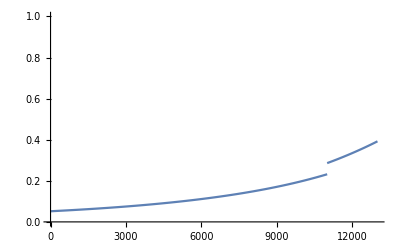

```mathematica
Show[highaccelfactor,lowaccelfactor]
```

```mathematica
transitionalt[mach_,descentcas_]:=3.28084FindMinimum[(mach  isasound[alt]-
descentcas/1.94384 Sqrt[1/densityratio[alt]])^2,alt][[2,1,2]]
```

```mathematica
transitionalts = Table[{.73+i .01, 240+j 10, transitionalt[.73+i .01,240+j 10]},{i,11},{j,8}];
```

```mathematica
ListPlot3D[Flatten[transitionalts,1],AxesLabel->{"Mach","CAS","Transition Alt(ft)"}]
```

-Graphics3D-

A function to assemble the data for descent from a cruise altitude

```mathematica
cruiseto10ktimedist[hcruise_,transitionalts_,machfun_,glidefun_]:= 
Table[
Flatten[

{
hcruise,
transitionalts[[i1,j1,3]],
If[(* Integrate from hcruise to transition alt if transitionalt less than Mach cruise *)
hcruise>transitionalts[[i1,j1,3]],
machdescenttimedist[hcruise, transitionalts[[i1,j1,3]],transitionalts[[i1,j1,1]], machfun],{0,0}],
 
If[ (* Integrate CAS from cruise or transitionalt, whichever is lowest *)
hcruise<transitionalts[[i1,j1,3]],

casdescenttimedist[ hcruise, 10000, transitionalts[[i1,j1,2]],glidefun],
casdescenttimedist[transitionalts[[i1,j1,3]],10000,transitionalts[[i1,j1,2]], glidefun]+
casdescenttimedist[hcruise,transitionalts[[i1,j1,3]],transitionalts[[i1,j1,2]],glidefun]],
(* Append deceleration data at 10k feet *)
slowdown777[[j1,2]],slowdown777[[j1,3]]
}

],{i1,9(*Dimensions[transitionalts][[1]]*)},{j1,8(*Dimensions[transitionalts][[2]]*)}
]
```

```mathematica
(* descents=Table[cruiseto10ktimedist[30000 + i 1000, transitionalts,machdata737, glidedata737],{i,10}];//Timing *)
```

```mathematica
descents>>descentprofiles;
```

```mathematica
descents=<<descentprofiles;
```

Create profile for {A/C type, Mach/CAS pair, A/C mass}

```mathematica
transaltpicker[mach_,cas_]:=transitionalttable[[Floor[100 (mach-0.74)]+1, (cas-250)/10+1,3]]
```

```mathematica
descentprofile[type_, mach_, cas_,mass_]:=
Module[{xzprofile,transalt,uppertransedge,lowertransedge,machpart,caspart,
maxmachindex,mincasindex, transmachportion},
{
xzprofile =Table[{0,13000-i 100, 0},{i,0,130}];transalt = transaltpicker[mach,cas];
uppertransedge=100 Ceiling[transalt/100];
lowertransedge=100 Floor[transalt/100];
maxmachindex=(13000-uppertransedge)/100;
mincasindex=(13000-lowertransedge)/100 +1;
transmachportion=(transalt-lowertransedge)/100.;

machpart=ToExpression[StringJoin["machdata",type,"m"]][mach,mass];
caspart= ToExpression[StringJoin["glidedata",type,"m"]][cas,mass];

Do[
{
xzprofile[[i,1]]=xzprofile[[i-1,1]]+machpart[[i-1,1]] machpart[[i-1,2]];
xzprofile[[i,3]]=xzprofile[[i-1,3]]+machpart[[i-1,1]]
},{i,2,maxmachindex}
];
xzprofile[[maxmachindex+1,1]]= (* Distance calculation *)xzprofile[[maxmachindex,1]]+machpart[[maxmachindex,1]] machpart[[maxmachindex,2]]transmachportion+caspart[[maxmachindex,1]]caspart[[maxmachindex,2]](1-transmachportion);
xzprofile[[maxmachindex+1,3]]=(* Time calculation *)xzprofile[[maxmachindex,3]]+machpart[[maxmachindex,1]]transmachportion+
caspart[[maxmachindex,1]] (1-transmachportion);
Do[
{
xzprofile[[i,1]]=xzprofile[[i-1,1]]+caspart[[i-1,1]] caspart[[i-1,2]];
xzprofile[[i,3]]=xzprofile[[i-1,3]]+caspart[[i-1,1]]
},{i,mincasindex,131}
];
};
xzprofile
]
```

```mathematica
Export["RickANZ777.xls", ricktable]
```

RickANZ777.xls

```mathematica
descentprofiles737lt = Table[descentprofile["737",0.74+ .01i,240 + 20 i,55000],{i,1,4}];
```

```mathematica
descentprofiles737hv = Table[descentprofile["737",0.74+.01 i,240 + 20 i,75000],{i,1,4}];
```

```mathematica
descentprofiles777lt = Table[descentprofile["777",0.80+.01 i,240 + 20 i,200000],{i,1,4}];
```

```mathematica
descentprofiles777hv = Table[descentprofile["777",0.80+.01 i,240 + 20 i,280000],{i,1,4}];
```

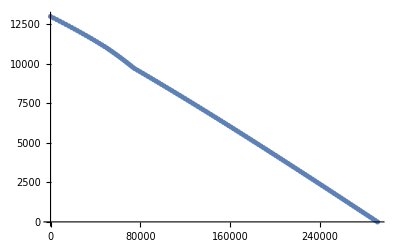

```mathematica
ListPlot[Table[{descentprofiles737lt[[1]][[i, 1]],descentprofiles737lt[[1]][[i, 2]]},{i,Length[descentprofiles737lt[[1]]]}]]
```

```mathematica
xzfit[data_]:=
Module[{xzdata},
{
xzdata=Table[{data[[i,1]]-data[[-1,1]],data[[i,2]]},{i,Length[data]}];
result=LinearModelFit[xzdata,x,x,IncludeConstantBasis->False]
};
Coefficient[Normal[result],x]
]
```

```mathematica
xtfit[data_]:=
Module[{xzdata},
{
xzdata=Table[{data[[i,1]]-data[[-1,1]],data[[i,3]]-data[[-1,3]]},{i,Length[data]}];
result=LinearModelFit[xzdata,{x,x^2},x,IncludeConstantBasis->False]
};
Take[CoefficientList[Normal[result],x],-2]
]
```

```mathematica
t1=Table[xzfit[descentprofiles737lt[[j]]],{j,4}]
t2=Table[xzfit[descentprofiles737hv[[j]]],{j,4}]
t3=Table[xzfit[descentprofiles777lt[[j]]],{j,4}]
t4=Table[xzfit[descentprofiles777hv[[j]]],{j,4}]
t5=Table[xtfit[descentprofiles737lt[[j]]],{j,4}]
t6=Table[xtfit[descentprofiles737hv[[j]]],{j,4}]
t7=Table[xtfit[descentprofiles777hv[[j]]],{j,4}]
t8=Table[xtfit[descentprofiles737hv[[j]]],{j,4}]
```

{-0.0454275,-0.0525883,-0.0603293,-0.0681748}

{-0.0408715,-0.0452477,-0.0503593,-0.055768}

{-0.0391977,-0.0426551,-0.0467291,-0.0516704}

{-0.0395099,-0.0403988,-0.0420931,-0.0447734}

{{0.00725021,6.28833×10^-9},{0.00664491,6.13431×10^-9},{0.00610367,5.71469×10^-9},{0.00562371,5.04343×10^-9}}

{{0.00726499,5.71095×10^-9},{0.00667525,5.39973×10^-9},{0.00614617,4.96342×10^-9},{0.00567196,4.37136×10^-9}}

{{0.00731432,5.83845×10^-9},{0.00676442,5.3442×10^-9},{0.00627202,4.91187×10^-9},{0.00583171,4.50928×10^-9}}

{{0.00726499,5.71095×10^-9},{0.00667525,5.39973×10^-9},{0.00614617,4.96342×10^-9},{0.00567196,4.37136×10^-9}}

```mathematica
XZprofilecoeffs={t1,t2,t3,t4}//MatrixForm
```

(-0.0454275 | -0.0525883 | -0.0603293 | -0.0681748
-0.0408715 | -0.0452477 | -0.0503593 | -0.055768
-0.0391977 | -0.0426551 | -0.0467291 | -0.0516704
-0.0395099 | -0.0403988 | -0.0420931 | -0.0447734)

```mathematica
SetDirectory["/Users/brucesawhill/Desktop"]
```

/Users/brucesawhill/Desktop

```mathematica
Export["XT.xls", XTprofilecoeffs];
```

```mathematica
XTprofilecoeffs={t5,t6,t7,t8}//MatrixForm
```

((0.00725021
6.28833×10^-9) | (0.00664491
6.13431×10^-9) | (0.00610367
5.71469×10^-9) | (0.00562371
5.04343×10^-9)
(0.00726499
5.71095×10^-9) | (0.00667525
5.39973×10^-9) | (0.00614617
4.96342×10^-9) | (0.00567196
4.37136×10^-9)
(0.00731432
5.83845×10^-9) | (0.00676442
5.3442×10^-9) | (0.00627202
4.91187×10^-9) | (0.00583171
4.50928×10^-9)
(0.00726499
5.71095×10^-9) | (0.00667525
5.39973×10^-9) | (0.00614617
4.96342×10^-9) | (0.00567196
4.37136×10^-9))

```mathematica
Export["XZ.xls",XZprofilecoeffs ]
```

XZ.xls

```mathematica
5/269
```

5/269

## FAA Calculations

Cruise speed of B738 for FAA

```mathematica
450 .5144
```

231.48

```mathematica
fb38=Table[fburn[38000/3.28084,124.65,.0254,.0358,.701, 1068,65300+ 1000 i,0,
231.48,0],{i,0,12}];
fb37=Table[fburn[37000/3.28084,124.65,.0254,.0358,.701, 1068,65300+ 1000 i,0,
231.48,0],{i,0,12}];
```

```mathematica
fb36=Table[fburn[36000/3.28084,124.65,.0254,.0358,.701, 1068,65300+ 1000 i,0,
231.48,0],{i,0,12}];
```

```mathematica
timedistlevelcruise38=Table[{1000/fb38[[i]],231.48 1000/fb38[[i]]},{i,13}];
timedistlevelcruise37=Table[{1000/fb37[[i]],231.48 1000/fb37[[i]]},{i,13}];
timedistlevelcruise36=Table[{1000/fb36[[i]],231.48 1000/fb36[[i]]},{i,13}];
```

```mathematica
timedistancecruisesum38=Table[{Sum[timedistlevelcruise38[[i,1]],{i,j}],Sum[timedistlevelcruise38[[i,2]],{i,j}], j 1000},{j,1,13}];
timedistancecruisesum37=Table[{Sum[timedistlevelcruise37[[i,1]],{i,j}],Sum[timedistlevelcruise37[[i,2]],{i,j}], j 1000},{j,1,13}];
timedistancecruisesum36=Table[{Sum[timedistlevelcruise36[[i,1]],{i,j}],Sum[timedistlevelcruise36[[i,2]],{i,j}], j 1000},{j,1,13}];
```

```mathematica
fueldist38=Fit[Table[Take[timedistancecruisesum38[[i]],{2,3}],{i,13}], {x,x^2},x]
fueldist37=Fit[Table[Take[timedistancecruisesum37[[i]],{2,3}],{i,13}], {x,x^2},x]
fueldist36=Fit[Table[Take[timedistancecruisesum36[[i]],{2,3}],{i,13}], {x,x^2},x]
```

0.00301089 x+4.75448×10^-11 x^2

0.00307491 x+4.61104×10^-11 x^2

0.00314321 x+4.48538×10^-11 x^2